```mathematica
λval=0.25;(*RANDOM NUMBER FOR QUENCHED DISORDER. FOR THIS VALUE OF λval, WE GET 25 % disorder ! *)
```

```mathematica
(*EAVAL=FRICTIONAL COUPLING IS CHANGED FROM 0.01 to 0.5. The system has a steady state solution, i.e. eigenvector with eigenvalue zero always. However, the band gap between the zero eigenvector and the non-zero eigenvector changes. Observe how the BAND GAP BETWEEN THE ZERO AND THE NEXT EIGENVALUES is slowly increased as EAVAL IS INCREASED in the three runs below. The first plot are the code snippet has the first 10 eigenvalues of the system.*)
```

{2.52625×10^-26+2.7903×10^-26 ⅈ}

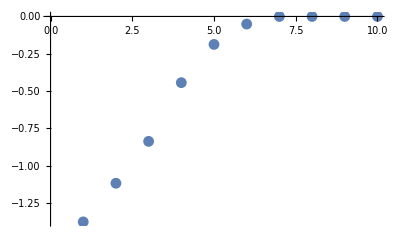

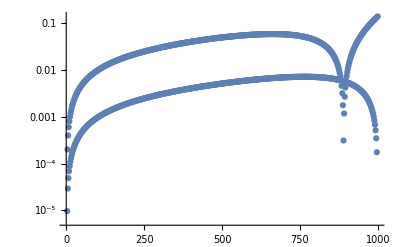

```mathematica
(*Subscript[λ, Ω]=t1,a=s1,b=b1,Subscript[λ, ω]=Ea,s2 Coefficient of \nabla^2 in Eq 3b. t1,b, and s2 have to be multiplied by 10000=1/\delta x^2 to accurately model the laplacian*)
(* s1 and b set dissipative coupling*)
(*value of \delta x=0.1, Box lenght=1000*0.1=100*)
Ntval=500;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=0.01;
s1val = 10;s2val =2000.0;
t1val = 2000;b1val = 100;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
(*ListLogPlot[Abs[Eigenvalues[WF1,-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->50000}]],PlotRange->All]*)
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->200,"MaxIterations"->50000}]],PlotRange->All]
(*ListPlot[Re[Eigenvalues[WF1]],PlotRange->All]*)
ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]],PlotRange->All]
(*ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]*)
(*Eigenvalues[WF1]*)
```

{9.37069×10^-25-7.50298×10^-25 ⅈ}

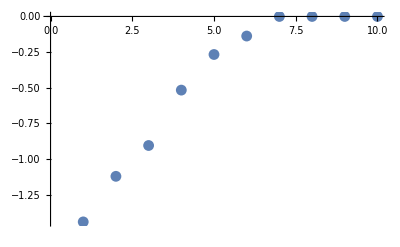

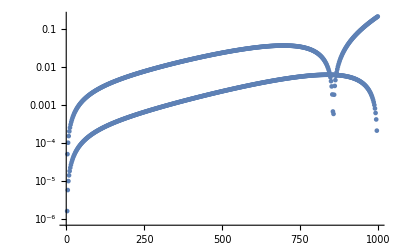

```mathematica
Ntval=500;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=0.1;
s1val = 10;s2val =2000.0;
t1val = 2000;b1val = 100;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
(*ListLogPlot[Abs[Eigenvalues[WF1,-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->50000}]],PlotRange->All]*)
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->200,"MaxIterations"->50000}]],PlotRange->All]
(*ListPlot[Re[Eigenvalues[WF1]],PlotRange->All]*)
ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]],PlotRange->All]
(*ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]*)
(*Eigenvalues[WF1]*)
```

```mathematica
.
```

{1.86237×10^-25-5.28148×10^-25 ⅈ}

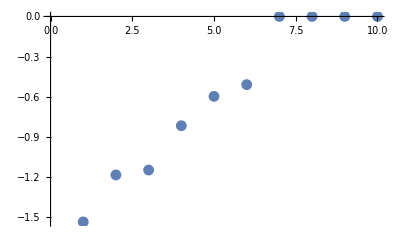

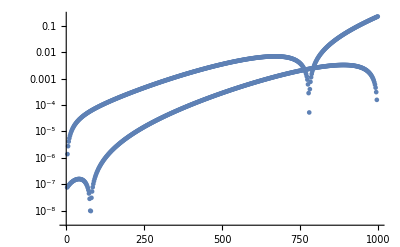

```mathematica
Ntval=500;h1val = 0.0; h2val = 0.0;h3val=0.0;h4val=0.0;Eaval=0.5;
s1val = 10;s2val =2000.0;
t1val = 2000;b1val = 100;
WF1=WRectangleAllLinksRotJ[s1val, s2val, t1val, b1val, h1val, h2val,h3val,h4val,Eaval,Ntval,   ⅈ λval];
Eigenvalues[WF1,-1,Method->{"Arnoldi","Criteria"->"Magnitude"}]
(*Eigenvalues[WF1,1,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->100,"MaxIterations"->10000}]*)
(*ListLogPlot[Abs[Eigenvalues[WF1,-10,Method->{"Arnoldi","Criteria"->"Magnitude","MaxIterations"->50000}]],PlotRange->All]*)
ListPlot[Re[Eigenvalues[WF1,10,Method->{"Arnoldi","Criteria"->"RealPart","BasisSize"->200,"MaxIterations"->50000}]],PlotRange->All]
(*ListPlot[Re[Eigenvalues[WF1]],PlotRange->All]*)
ListLogPlot[Abs[Eigenvectors[WF1][[2*Ntval]]],PlotRange->All]
(*ListLogPlot[Abs[Eigenvectors[Transpose[WF1]][[2*Ntval]]],PlotRange->All]*)
(*Eigenvalues[WF1]*)
```

```mathematica
SeedRandom[]
```

```mathematica
Ceven[x1_,y1_,k_,λ_]:=x1 Exp[λ/2]-y1 Exp[-λ/2]*Exp[I k] ;
Codd[x2_,y2_,k_,λ_]:=y2 Exp[λ/2]-x2 Exp[-λ/2]*Exp[I k] ;
factor[k_,λ_]:=-Exp[-λ/2]+Exp[-  I k +λ/2];
Wp1[x1_,y1_,x2_,y2_,k_,λ_]:={{Ceven[x1,y1,k,λ],0},{0,Codd[x2,y2,k,λ]}}
W0p1[k_,λ_]:={{factor[k,λ],0},{0,factor[k,λ]}}
WBp[b1_,b2_]:={{-b1,b2},{b1,-b2}}
Wperiodic[x1_,y1_,x2_,y2_,b1_,b2_,λ_,k_]:=Wp1[x1,y1,x2,y2,k,λ]+Inverse[W0p1[k,λ]].WBp[b1,b2]
```

```mathematica
MatrixForm[Wperiodic[x1,y1,x2,y2,b1,b2,λ,k]]
```

(-(b1 (ⅇ^(-ⅈ k+λ/2)-ⅇ^(-λ/2)))/(-2 ⅇ^(-ⅈ k)+ⅇ^-λ+ⅇ^(-2 ⅈ k+λ))+ⅇ^(λ/2) x1-ⅇ^(ⅈ k-λ/2) y1 | (b2 (ⅇ^(-ⅈ k+λ/2)-ⅇ^(-λ/2)))/(-2 ⅇ^(-ⅈ k)+ⅇ^-λ+ⅇ^(-2 ⅈ k+λ))
(b1 (ⅇ^(-ⅈ k+λ/2)-ⅇ^(-λ/2)))/(-2 ⅇ^(-ⅈ k)+ⅇ^-λ+ⅇ^(-2 ⅈ k+λ)) | -(b2 (ⅇ^(-ⅈ k+λ/2)-ⅇ^(-λ/2)))/(-2 ⅇ^(-ⅈ k)+ⅇ^-λ+ⅇ^(-2 ⅈ k+λ))-ⅇ^(ⅈ k-λ/2) x2+ⅇ^(λ/2) y2)

```mathematica
WindingRot1[x1_,y1_,x2_,y2_,b1_,b2_,λ_]:=Table[{Re[Det[Conjugate[Wperiodic[x1,y1,x2,y2,b1,b2,λ,i]]]],Im[Det[Conjugate[Wperiodic[x1,y1,x2,y2,b1,b2,λ,i]]]]},{i,-π,π,0.001}]
WindingRot2[x1_,y1_,x2_,y2_,b1_,b2_,λ_]:=Table[{i/(2*π),Im[Log[Det[Conjugate[Wperiodic[x1,y1,x2,y2,b1,b2,λ,i]]]]]},{i,-π,π,0.01}]
WindingRot3[x1_,y1_,x2_,y2_,b1_,b2_,λ_]:=Table[{i,Re[Det[Conjugate[Wperiodic[x1,y1,x2,y2,b1,b2,λ,i]]]]},{i,0,π,0.001}]
WindingRot4[x1_,y1_,x2_,y2_,b1_,b2_,λ_]:=Table[{i,Im[Det[Conjugate[Wperiodic[x1,y1,x2,y2,b1,b2,λ,i]]]]},{i,-π,π,0.001}]
```

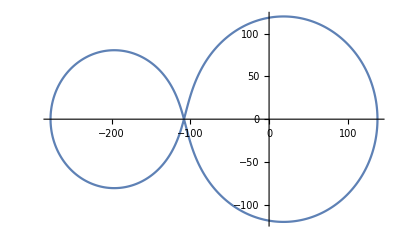

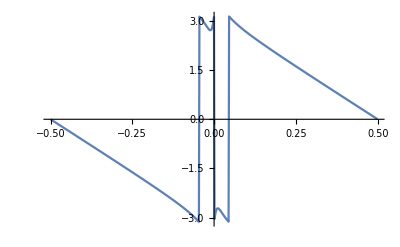

```mathematica
ListPlot[WindingRot1[10,1,10,1,2,1,-0.05],Joined->True]
ListPlot[WindingRot2[10,1,10,1,2,1,-0.05],PlotRange->All,Joined->True]
```